## DNA (λ̂)_00 Eigenvalue Analysis

/home/hemant/Desktop/workspace/Thesis/Results/DNA/Eigensystem/T00

0.5

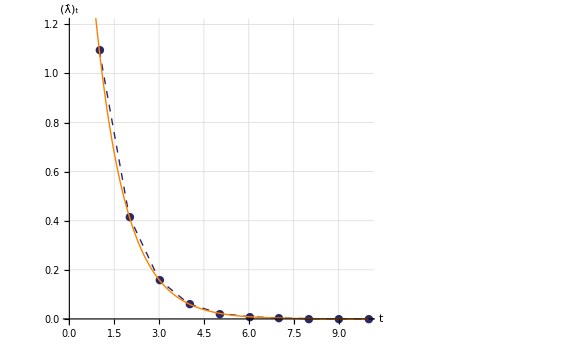

CreateDirectory::filex: "/home/hemant/Desktop/workspace/Thesis/Results/DNA/Eigensystem/T00/0.5/" already exists.

/home/hemant/Desktop/workspace/Thesis/Results/DNA/Eigensystem/T00/0.5

0.5/lambda_t_L50_m50.pdf

```mathematica
Needs["PlotLegends`"]
SetDirectory[FileNameJoin[{NotebookDirectory[]}]]

L=50;
m=50;
Δ=L/(2 m)//N
σ=1;
κ=1;
LastEval=10;

ηb=2L;

(*Numerical*)
V[η_]:=If[Abs[η]≤ηb,(σ η^2)/κ,(σ ηb^2)/κ];
g[μ_,η_]:=If[μ==0,
If[Abs[η]<ηb,1,0],
If[μ==1,
If[Abs[η]>ηb,1,0],
"μ has to be either 1 or 0"
]
];
T̂[μ1_, μ2_, η1_,η2_] :=   g[μ1, η1] g[μ2, η2]*Exp[-(η1 - η2)^2]*Exp[-(V[η1] + V[η2])/2];
Subscript[MT, 00] = Table[Δ T̂[ 0,0,Δ R1, Δ R2],{R1, -m, m}, {R2, -m, m}] // N;
Subscript[Mλ, t] = Eigenvalues[Subscript[MT, 00]];


(*Analytical*)

β=4;
μ=(2 σ)/κ//N;
c=((μ^2+2 β μ)^(1/2))/2//N;
Subscript[C, 0]=1/2 ((2 π)/((μ^2+2 β μ)^(1/2)))^(-1/4);
δ=2 c+μ+β;
b=1/2 ((δ^2-β^2)/δ)^(1/2)//N;
k=Log[δ/β]//N;
Subscript[e, 0]=((4 π)/δ)^(1/2)//N;
Subscript[MAλ, t][h_]:=Subscript[e, 0]*Exp[-k (h-1)];(*the -1 is to adjust the x-plot on the graph*)
nC[n_]:=(1/(2^n Factorial[n]))^(1/2);
Subscript[ψ̂, t][n_,η_]:=Subscript[C,0] nC[n] HermiteH[n,b η] Exp[-(c η^2)/2];

fsAxesLabel=24;
fs2=18;

p1 = ListLinePlot[Subscript[Mλ, t],PlotStyle -> {Thick, Dashed, Darker[ColorData[1, 1]]}, PlotMarkers -> {"●"}, PlotRange -> {{0,10},{0,1.2}}];
p2 = Plot[Subscript[MAλ, t][x], {x, 0, 10}, PlotStyle -> {Thick,Orange},PlotRange -> All];
{p1,p2};

legend = {{Graphics[{Thick, Dashed, Darker[ColorData[1, 1]], PointSize[Large],Point[{1, 0}], Line[{{0, 0}, {2, 0}}]}],  Style["Numerical", 
     FontSize -> fs2]}, {Graphics[{Thick, Orange,Line[{{0, 0}, {2, 0}}]}], Style["Analytical", FontSize -> fs2]}};
EvalPlotλ =  ShowLegend[ Show[{p1, p2}, PlotRange -> {{0,10},{0,1.2}}, ImageSize -> Large,  (*PlotLabel ->  Style["Eigenvalue (λ̂)_t Plot (L="<>ToString[L]<>" m="<>ToString[m]<>")", FontSize -> fsTitle],*) GridLines -> Automatic, 
   GridLinesStyle -> Directive[LightGray, Dashed], AxesLabel -> {Style["t", FontSize -> fsAxesLabel],   Style["(λ̂)_t", FontSize -> fsAxesLabel]}, 
   LabelStyle -> {"Times", FontSize -> fs2},  ImageSize -> Large], {legend, LegendShadow -> None,    LegendBorder -> None, LegendBackground -> Opacity[0], 
   ShadowBackground -> Opacity[0], LegendSize -> 0.5,    LegendPosition -> {0.1, 0.1}}]

CreateDirectory[ToString[Δ]]
Export[ToString[Δ]<>"/lambda_t_L"<>ToString[L]<>"_m"<>ToString[m]<>".pdf",EvalPlotλ]
```

Comparison of Eigenvalues - Numerical and Analytical

```mathematica
(*
5,10
10,20
20,40
30,60

5,20
10,40
20,80
30,120

5,40
10,80
20,160
30,240
*)
```